```mathematica
Remove["Global`*"]
```

```mathematica
(*WPM=40;WPL=30;WPP=15;*)
```

```mathematica
p = 4.0; V0=5.55702*10^(-10);mu=15.0;
ϕ0=7.3; dϕ0=8*10^(-7);Ni=0;Nf=70;
```

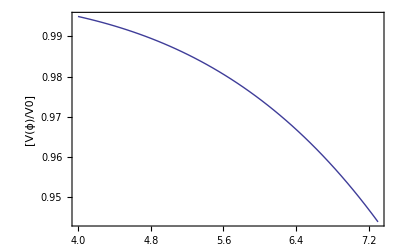

```mathematica
V[ϕ_] = V0*(1-(ϕ/mu)^p);
DV[ϕ_] = D[V[ϕ],ϕ];
Plot[(V[ϕ]/V0),{ϕ,ϕ0,4},PlotRange->All,Frame->True, FrameLabel->{"[V(ϕ)/V0]"}]
```

```mathematica
H0 = ((1/3)*((dϕ0^2/2)+V[ϕ0]))^(1/2);
Dϕ0 = (dϕ0/H0);
```

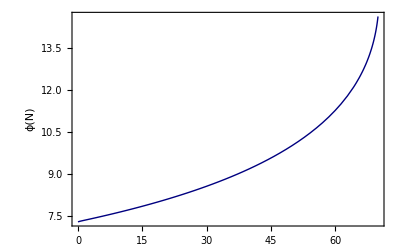

```mathematica
ϕSoln=NDSolve[{ϕ''[N1]+(3-ϕ'[N1]^2/2)*ϕ'[N1]+(DV[ϕ[N1]]/(2*V[ϕ[N1]]))*(6-(ϕ'[N1])^2)==0,ϕ[Ni]==ϕ0,ϕ'[Ni]==Dϕ0},ϕ,{N1,Ni,Nf},MaxSteps->1000000];
ϕ[N1_]=ϕ[N1]/.Flatten[ϕSoln];
Plot[ϕ[N1],{N1,Ni,Nf},Frame->True,PlotRange->All,FrameLabel->{"ϕ(N)"},PlotStyle->{Darker[Blue,0.5]}]
```

```mathematica
toFile = Flatten[Table[{" ",N[N1,10] ,N[ϕ[N1],10] ," "},{N1,Ni,Nf,(Nf-Ni)/100000}]]
Export["~/Github/project_work/small_field/data_files/phi_vs_N_mathematica.txt",toFile];
```

{ ,0,7.3, , ,0.0007,7.30004, , ,0.0014,7.30008, , ,0.0021,«399977», , ,69.9986,14.6328, , ,69.9993,14.6338, , ,70.,14.6348, }

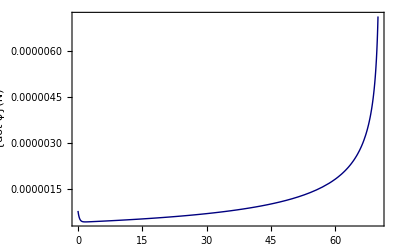

```mathematica
H[N1_]=(V[ϕ[N1]]/(3-((ϕ'[N1])^2)/2))^(1/2);
Plot[{H[N1]*ϕ'[N1]},{N1,Ni,Nf},Frame->True, PlotRange->All, FrameLabel->{"{dot ϕ}(N)"},PlotStyle->{Darker
[Blue,0.5]}]
```

```mathematica
toFile =Flatten[Table[{" ",N[N1,10],N[H[N1],10]," "},{N1,Ni,Nf,(Nf-Ni)/100000}]];
Export["~/Github/project_work/small_field/data_files/H_vs_N_mathematica.txt",toFile];
```

```mathematica
toFile = Flatten[Table[{" ",N[N1,10],N[H'[N1]*10^6,10]," "},{N1,Ni,Nf,(Nf-Ni)/100000}]];
Export["~/Github/project_work/small_field/data_files/DH_vs_N_mathematica.txt",toFile];
```

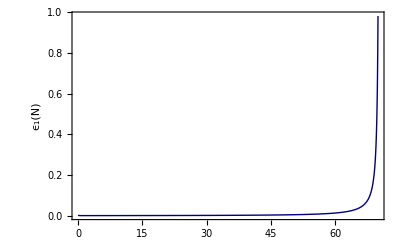

```mathematica
ϵ1[N1_] =((ϕ'[N1])^2/2);
Plot[ϵ1[N1],{N1,Ni,Nf},Frame->True, PlotRange->All, AspectRatio->0.6,FrameLabel->{"\!\(\*SubscriptBox[\(ϵ\),\(1\)]\)(N)"},PlotStyle->{Darker[Blue, 0.5]}]
```

```mathematica
toFile=Flatten[Table[{" ",N[N1,10],N[ϵ1[N1],10]," "},{N1,Ni,Nf,(Nf-Ni)/100000}]];
Export["~/Github/project_work/small_field/data_files/eps_vs_N_mathematica.txt",toFile];
```

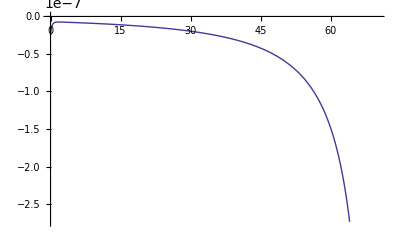

```mathematica
Plot[H'[N1],{N1,Ni,Nf}]
```

```mathematica
ai = 10^(-5);
A[N1_] = ai*Exp[N1]
```

ⅇ^N1/100000

```mathematica
toFile = Flatten[Table[{k = 10^(y);N[k,10],
Nics=N1/.FindRoot[k==(10^2*A[N1]*H[N1]),{N1,Ni,Nf}];N[Nics],
Nshss=N1/.FindRoot[k==(10^(-3)*A[N1]*H[N1]),{N1,Ni,Nf}];N[Nshss],
hkSoln = NDSolve[{hk''[N1]+hk'[N1]*(H'[N1]/H[N1]+3)+hk[N1]*(k/(H[N1]*A[N1]))^2==0, hk[Nics]==1/((2*k)^(1/2)*A[Nics]),hk'[Nics]==-I*(k/2)^(1/2)/(A[Nics]^2*H[Nics])-1/(A[Nics]*(2*k)^(1/2))},hk,{N1,Nics,Nshss}, InterpolationOrder->All,MaxSteps->10000000];
(*hk[N_] = hk[N]/.hkSoln;*)
N[2*(k^3/(2*Pi^2))*(Abs[hk[Nshss]/.Flatten[hkSoln]]^2)]*10^(10)},{y,-(60/10),-(0/10),1/2}]]
```

{1.×10^-6,4.32832,15.8496,0.0875823,3.16227766×10^-6,5.48031,17.0019,0.0874385,0.00001,6.63234,18.1543,0.0872894,0.0000316227766,7.78439,19.3067,0.0871347,0.0001,8.93646,20.4592,0.0869743,0.000316227766,10.0886,21.6117,0.0868077,0.001,11.2407,22.7642,0.0866347,0.00316227766,12.3929,23.9169,0.0864548,0.01,13.5451,25.0696,0.0862677,0.0316227766,14.6973,26.2223,0.0860729,0.1,15.8496,27.3751,0.0858707,0.316227766,17.0019,28.5281,0.0856637,1.,18.1543,29.681,0.0854317}

```mathematica
Export["~/Github/project_work/small_field/data_files/tps_mathematica.txt",toFile]
```

~/Github/project_work/small_field/data_files/tps_mathematica.txt